```mathematica
(1/(80*365))/((1/(80*365))+1/22)
```

11/14611

```mathematica
S=(1/R)-(2p/((R-1)+√((R-1)^2+4*R*p)))
```

1/R-(2 p)/(-1+R+√((-1+R)^2+4 p R))

```mathematica
V=(ϵ*(R-1)+ϵ*√((R-1)^2+4*R*p))/(2*R)
```

((11 (-1+R))/14611+(11 √((-1+R)^2+4 p R))/14611)/(2 R)

```mathematica
ϵ=11/14611
```

11/14611

```mathematica
Solve[(1-R S+R V+ϵ)^2-4 (R V+ϵ-R S ϵ)==0,p]
```

{{p→1/(11427918301679364 R^2)(-68518576720000 R+77218944757482 R^2-8590653329841 R^3-40 √11732633 √(-20605858095536839300 R^2+62035581180294517551 R^3-62254293855155321400 R^4+20824571409399990000 R^5))},{p→1/(11427918301679364 R^2)(-68518576720000 R+77218944757482 R^2-8590653329841 R^3+40 √11732633 √(-20605858095536839300 R^2+62035581180294517551 R^3-62254293855155321400 R^4+20824571409399990000 R^5))}}

```mathematica
Clear[p]
```

```mathematica
g[R_]:=1/(11427918301679364 R^2)(-68518576720000 R+77218944757482 R^2-8590653329841 R^3+40 √11732633 √(-20605858095536839300 R^2+62035581180294517551 R^3-62254293855155321400 R^4+20824571409399990000 R^5))
```

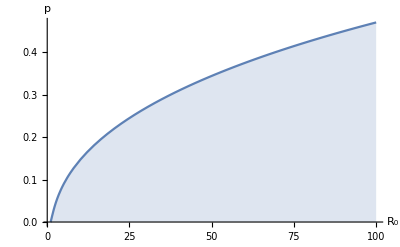

```mathematica
Plot[g[R],{R,0,100},Filling->Bottom,AxesLabel->{Subscript[R, 0],p},PlotRange->All]
```

```mathematica
h[R_]:=g[R+1]
```

LogLinearPlot::invpr: Value of option PlotRange should be positive in the scaled dimensions.

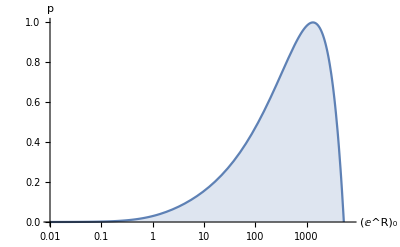

```mathematica
LogLinearPlot[h[R],{R,0.01,7000},Filling->Bottom,AxesLabel->{Subscript[R, 0],p},PlotRange->{{0,7000},{0,1}}]
```

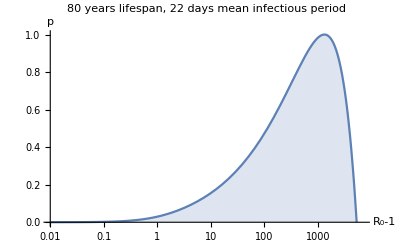

```mathematica
Show[%8,AxesLabel->{HoldForm[Subscript[R, 0]-1],p},PlotLabel->RawBoxes[RowBox[{RowBox[{"80"," ","years"," ","lifespan"}],","," ",RowBox[{"22"," ","days"," ","mean"," ","infectious"," ","period"}]}]],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["C:\\Users\\Roger Zhang\\Desktop\\Figures\\p_vs_R_0\\80_22.pdf",%48,"PDF"]
```

C:\Users\Roger Zhang\Desktop\Figures\p_vs_R_0\80_22.pdf